```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B2thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-(1+nb[Epi[q,mp2],T])/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[Epi[q,mp2],T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))-nb[Epi[q,mp2],T]/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[Epi[q,mp2],T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))-nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q,mp2]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2)^2)-(-1+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((1+nb[Epi[q,mp2],T]) (-Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2)^2)-(nb[Epi[q,mp2],T] (Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2)^2));
Zpsi[mp2_,mf2_,h_,p0_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(3 π^2)NIntegrate[q^4 Re[F1B2thr[mp2,mf2,p0,q,T,mu]],{q,1,2000}]+1
```

```mathematica
fpidata=Transpose[Import["../../../sigma0.dat"]];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
T=Table[i,{i,10,250,20}];
```

```mathematica
T1=70;
mpi=Flatten[Table[√(Flatten[Import["../input/T"<>ToString[T1]<>"/sigma"<>ToString[i]<>".dat"]][[1]]),{i,5,400,5}]];
data=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]]],{i,1,80}]
Export["./T"<>ToString[T1]<>"/Zpsi.dat",data]
```

{1.33275,1.33276,1.33278,1.33281,1.33284,1.33288,1.33293,1.33298,1.33305,1.33311,1.33319,1.33327,1.33336,1.33345,1.33355,1.33365,1.33376,1.33387,1.33398,1.3341,1.33422,1.33434,1.33447,1.33459,1.33471,1.33483,1.33495,1.33507,1.33517,1.33527,1.33536,1.33544,1.33551,1.33555,1.33558,1.33558,1.33556,1.33549,1.33539,1.33524,1.33503,1.33474,1.33437,1.33389,1.33326,1.33247,1.33144,1.3301,1.32832,1.32592,1.32257,1.31786,1.3114,1.30349,1.29503,1.28676,1.27892,1.27156,1.26466,1.25816,1.25202,1.2462,1.24067,1.2354,1.23037,1.22554,1.22092,1.21647,1.21219,1.20806,1.20408,1.20023,1.1965,1.19289,1.18939,1.18599,1.1827,1.17949,1.17637,1.17334}

./T70/Zpsi.dat

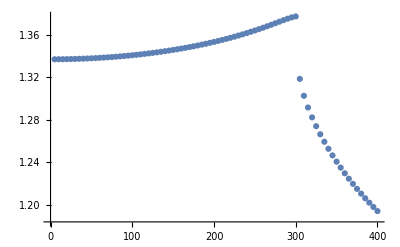

```mathematica
ListPlot[Transpose[{mu,data}]]
```